## Probabilidad - Ejercitación

Distribución Binomial

La distribución binomial es un tipo de distribución de probabilidad discreta que se utiliza para modelar experimentos o eventos que tienen dos resultados posibles: éxito o fracaso. Estos eventos deben cumplir con dos condiciones clave:

1. Cada intento o experimento es independiente del anterior.
2. La probabilidad de éxito, denotada como “p” es constante en cada intento.

Los parámetros principales de una distribución binomial son 

	•   n : el número total de intentos o ensayos
	•  p :  la probabilidad de éxito en un solo intento

Sabemos que la función de probabilidad de una distribución binomial se define como:

							P(X = r) =  (n!)/(r! * (n-r)!)  p^r (1-p)^(n-r)  
Donde:

	• P(X = r es la probabilidad de que ocurran exactamente “r” éxitos en “n” ensayos.
	•  (n!)/(r! * (n-r)!) = (n
r) es el coeficiente binomial, que calcula el número de formas en que “r” éxitos pueden ocurrir en “n” ensayos.
	• p es la probabilidad de éxito en un solo intento.
	• (1 - p ) es la probabilidad de fracaso en un solo intento.

Aproximación Normal a la Distribución Binomial

Cuando 

	•  el número de ensayos n es grande
	•  la probabilidad de éxito p no es muy pequeña

la distribución binomial se puede aproximar mediante una distribución normal. Esta aproximación se basa en el Teorema del Límite Central.

El Teorema del Límite Central establece que, cuando se suman un gran número de variables aleatorias independientes y con la misma distribución, su suma se distribuye aproximadamente de manera normal, independientemente de la forma de la distribución original. En el caso de la distribución binomial, podemos considerar cada intento como una variable aleatoria independiente y sumarlas para obtener el resultado total.

La aproximación normal a la distribución binomial se expresa como:

				X ~ N(μ, σ^2)
Donde:
	- μ = n · p es la media de la distribución binomial.
	- σ^2 = n · p · (1 - p)  es la varianza de la distribución binomial.

Entonces, cuando “n” es lo suficientemente grande, la distribución binomial se asemeja cada vez más a una distribución normal. Esto significa que podemos utilizar las propiedades de la distribución normal, como la regla empírica o la tabla Z, para hacer cálculos y estimaciones sobre la distribución binomial.

Veamos un ejemplo!

```mathematica
n=100 (*Número de intentos*);p=0.5(*Probabilidad de éxito en un solo intento*);data=RandomVariate[BinomialDistribution[n,p],1000](*Generar una muestra de la distribución binomial*);
```

Ahora calculamos la media y la desviación estándar de la distribución binomial y creamos la aproximación a distribución normal!

```mathematica
mean=n*p;
stddev=Sqrt[n*p*(1-p)];

normalDist=NormalDistribution[mean,stddev]; (*aproximación normal*)


normalData=RandomVariate[normalDist,1000]; (*muestra de distribución normal*)
```

Ahora, grafiquemos esto para poder visualizarlo...

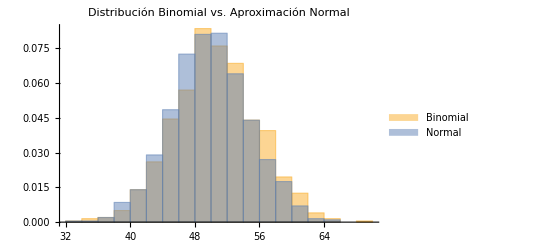

```mathematica
(*Mostrar un histograma de la distribución binomial y la aproximación normal*)
Histogram[{data,normalData},Automatic,"PDF",PlotLabel->"Distribución Binomial vs. Aproximación Normal",ChartLegends->{"Binomial","Normal"}]
```

El histograma muestra la distribución binomial y la aproximación normal. Como podemos ver, a medida que n se hace más grande, la distribución binomial se parece cada vez más a la distribución normal. En este caso, con “n = 100”, ya podemos apreciar una buena aproximación. Veámoslo con otros valores...

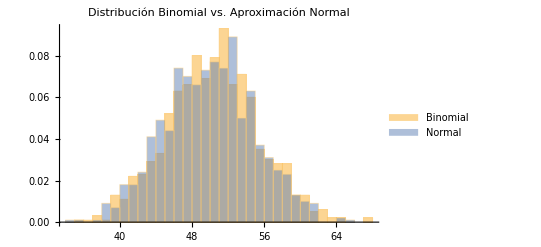

```mathematica
n=100;p=0.5;data=RandomVariate[BinomialDistribution[n,p],1000];
mean=n*p;
stddev=Sqrt[n*p*(1-p)];
normalDist=NormalDistribution[mean,stddev];
normalData=RandomVariate[normalDist,1000];
Histogram[{data,normalData},Automatic,"PDF",PlotLabel->"Distribución Binomial vs. Aproximación Normal",ChartLegends->{"Binomial","Normal"}]
```

```mathematica
p=0.5;Manipulate[Histogram[{RandomVariate[BinomialDistribution[n,p],1000],RandomVariate[NormalDistribution[n*p,Sqrt[n*p*(1-p)]],1000]},Automatic,"PDF",PlotLabel->"Distribución Binomial vs. Aproximación Normal",ChartLegends->{"Binomial","Normal"}],{n,1,100,1}]
```

## Repartido de Ejercicios Nro 1

7. Tres tiradores A, B y C disparan contra un blanco. Las probabilidades de acertar son: p(A) = 0,75; p(B) = 0,80; p(C) = 0,90.
Hallar la probabilidad de que:

	(a) Ninguno dé en el blanco.

	(b) Al menos uno de ellos dé en el blanco.

	(c) Dos de ellos exactamente den en el blanco.

9.  Un viaje científico a la Antártida se realiza con aviones bimotores o cuadrimotores. Los bimotores pueden volar con un solo motor y los cuadrimotores con dos. La probabilidad de que un motor falle durante la travesía es 5%. ¿Cuáles aviones son más seguros? ¿y si la probabilidad de que un motor falle es p?

11. Un meteorólogo anunció que la probabilidad de que llueva en un día cualquiera de Septiembre
es p = 1/3 y es independiente de lo sucedido en días anteriores.

	(a) Calcular la probabilidad de que en la primer semana de setiembre llueva exactamente 5 días.

	(b) Calcular la probabilidad de que llueva 5 o más días.